## Rubin 2015 model

```mathematica
stims[l_,x_]:=(1/(1+Exp[-(x+l/2)/σRF]))(1-1/(1+Exp[-(x-l/2)/σRF]))
```

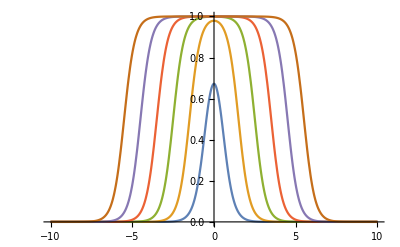

```mathematica
Plot[Evaluate@Table[stims[l,x]/.{σRF->0.33},{l,1,12,2}],{x,-10,10},PlotRange->All]
```

## Spatial problem (1 population)

there are 4 cells per degree

```mathematica
Δx=0.25;(*degrees/ncells*)
Δ=Δx^-1; (*ncells/degree*)
Nn=IntegerPart[26Δ];(*from -5 to 5 times Δx=4*)
cent=Nn/2;
σFF=(0.33Δ)^2;(*this is the variance*)
σEE=(0.5Δ)^2;
σIE=(1Δ)^2;
σEI=(0.01)^2;
σII=(0.01)^2;
c=1;
(*G[z_,s_]:=1/Sqrt[2π s] Exp[-z^2/(2s)];(*fix normalization because it is discrete*)*)
(*H=h0 Table[G[z-cent,σFF],{z,0,Nn}];*)
G[z_,s_]:=Exp[-z^2/(2s)];
H[l_]:=c Table[(1/(1+Exp[-(x+l/2)/σFF]))(1-1/(1+Exp[-(x-l/2)/σFF])),{x,-Nn/2,Nn/2}]
HG[l_]:=c Table[Exp[-x^2/(2(0.5 l)^2)],{x,-Nn/2,Nn/2}];
WEE=.385 Table[G[z-y,σEE],{z,0,Nn},{y,0,Nn}];
WIE=1 Table[G[z-y,σIE],{z,0,Nn},{y,0,Nn}];
WEI=-.55 Table[G[z-y,σEI],{z,0,Nn},{y,0,Nn}];
WII=-1.5 Table[G[z-y,σII],{z,0,Nn},{y,0,Nn}];
s=10Δ;
```

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.125] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-20000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-45000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-20000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-45000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
(*l is in steps=degrees*Δ*)
```

plot input and connectivity

```mathematica
(*Row[{Show[{ListPlot[H,PlotRange->All,ImageSize->300,DataRange->{0,Nn},AxesLabel->{"space","input current"}],Plot[h0 G[(z-cent),σFF]/.h0->1,{z,0,30}]}],MatrixPlot[WEE,PlotLegends->Automatic,ImageSize->150,PlotLabel->"EE connectivity"]}]*)
```

104

-1.5

0.

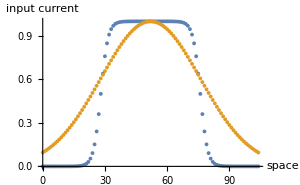
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
s=12Δ;
Nn
WII[[1,1]]
WII[[1,3]]
Row[{ListPlot[{H[s],HG[s]},PlotRange->All,ImageSize->300,DataRange->{0,Nn},AxesLabel->{"space","input current"}],MatrixPlot[WEE,PlotLegends->Automatic,ImageSize->150,PlotLabel->"EE connectivity"],MatrixPlot[WIE,PlotLegends->Automatic,ImageSize->150,PlotLabel->"IE connectivity"],MatrixPlot[WEI,PlotLegends->Automatic,ImageSize->150,PlotLabel->"EI connectivity"],MatrixPlot[WII,PlotLegends->Automatic,ImageSize->150,PlotLabel->"II connectivity"]}]
```

```mathematica
ϕ[x_]:=HeavisideTheta[x] x^2;
(*ϕ[x_]:=x^2;*)
f[x_List?(Length[#]==Nn+1&)]:=Map[ϕ,x];
Clear[X,Y];
tmax=40;
sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+H[s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+H[s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];
```

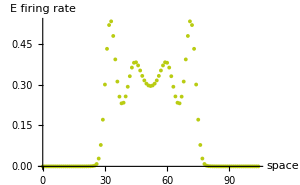
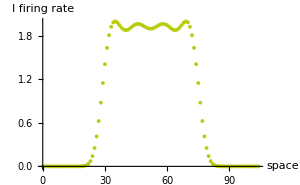

```mathematica
tmax=40;
Row[{ListPlot[Evaluate[sol[[1]][tmax]],DataRange->{0,Nn},PlotRange->All,AxesLabel->{"space","E firing rate"},PlotStyle->ColorData[10]@5,ImageSize->300],ListPlot[Evaluate[sol[[2]][tmax]],DataRange->{0,Nn},PlotRange->All,AxesLabel->{"space","I firing rate"},PlotStyle->ColorData[10]@5,ImageSize->300]}]
```

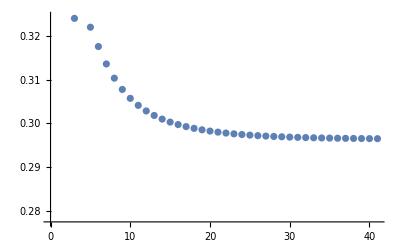

```mathematica
ListPlot[Table[Evaluate[sol[[1]][t]][[IntegerPart[Nn/2]]],{t,0,tmax}]]
```

```mathematica
Clear[X,Y,s];
tmax=40;
(*stcE2=ConstantArray[.1,12];
stcI2=ConstantArray[.1,12];*)
For[s=9,s<10,s++,{sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+H[Δ s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+H[Δ s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];stcE2[[s]]=Evaluate[sol[[1]][tmax]][[IntegerPart[Nn/2]]];stcI2[[s]]=Evaluate[sol[[2]][tmax]][[IntegerPart[Nn/2]]];}]
```

```mathematica
ss={1,2,3,4,5,6,7,8,9,3Δ,4Δ,5Δ,6Δ,7Δ,8Δ,9Δ,10Δ,11Δ,12Δ};
```

```mathematica
stE=Join[stcE[[1;;9]],stcE2[[3;;]]]
stI=Join[stcI[[1;;9]],stcI2[[3;;]]]
```

{0.109317,0.169826,0.243396,0.324759,0.406968,0.482911,0.546558,0.593477,0.620731,0.572639,0.314219,0.181042,0.214078,0.343719,0.423826,0.390961,0.310655,0.274823,0.29653}

{0.22763,0.37463,0.56084,0.774891,1.00139,1.22448,1.43074,1.61057,1.75821,1.9955,1.99252,1.92958,1.85134,1.8725,1.95303,1.97668,1.94985,1.91628,1.90053}

```mathematica
Export["/Users/serena/Dropbox/RubinsizetuningE.csv",stE];
Export["/Users/serena/Dropbox/RubinsizetuningI.csv",stI];
```

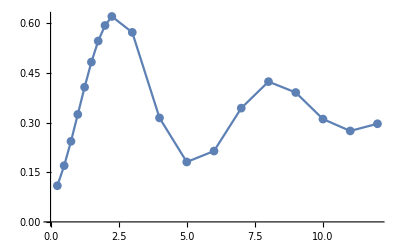

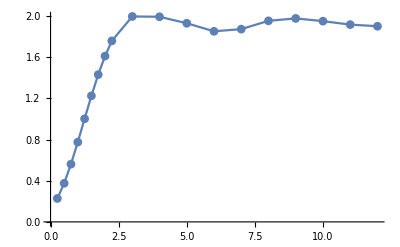

```mathematica
ListPlot[Table[{ss[[i]]/Δ,stE[[i]]},{i,1,Length[ss]}],Joined->True,PlotMarkers->Automatic]
ListPlot[Table[{ss[[i]]/Δ,stI[[i]]},{i,1,Length[ss]}],Joined->True,PlotMarkers->Automatic]
```

## Gaussian input

```mathematica
ϕ[x_]:=HeavisideTheta[x] x^2;
(*ϕ[x_]:=x^2;*)
f[x_List?(Length[#]==Nn+1&)]:=Map[ϕ,x];
Clear[X,Y];
tmax=40;
sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+HG[s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+HG[s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];
```

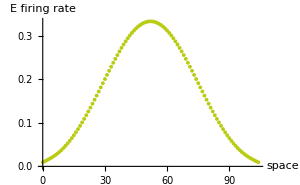
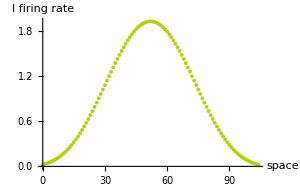

```mathematica
tmax=40;
Row[{ListPlot[Evaluate[sol[[1]][tmax]],DataRange->{0,Nn},PlotRange->All,AxesLabel->{"space","E firing rate"},PlotStyle->ColorData[10]@5,ImageSize->300],ListPlot[Evaluate[sol[[2]][tmax]],DataRange->{0,Nn},PlotRange->All,AxesLabel->{"space","I firing rate"},PlotStyle->ColorData[10]@5,ImageSize->300]}]
```

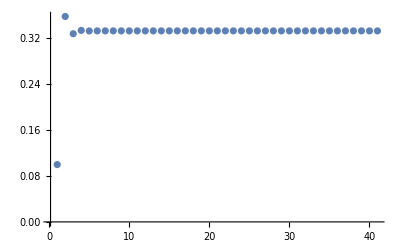

```mathematica
ListPlot[Table[Evaluate[sol[[1]][t]][[IntegerPart[Nn/2]]],{t,0,tmax}],PlotRange->All]
```

```mathematica
Clear[X,Y,s];
tmax=20;
stcEG=ConstantArray[.1,12];
stcIG=ConstantArray[.1,12];
For[s=1,s<13,s++,{sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+HG[Δ s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+HG[Δ s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];stcEG[[s]]=Evaluate[sol[[1]][tmax]][[IntegerPart[Nn/2]]];stcIG[[s]]=Evaluate[sol[[2]][tmax]][[IntegerPart[Nn/2]]];Print[stcEG];Print[stcIG];}]
```

```mathematica
ssG={Δ,2Δ,3Δ,4Δ,5Δ,6Δ,7Δ,8Δ,9Δ,10Δ,11Δ,12Δ};
```

```mathematica
stcEG
stcIG
```

{0.855462,0.836821,0.601117,0.436276,0.377686,0.357293,0.347823,0.342328,0.338793,0.336361,0.334607,0.333296}

{1.87682,2.21762,2.12642,2.01951,1.97418,1.95535,1.94607,1.94067,1.93719,1.93481,1.9331,1.93182}

```mathematica
Export["/Users/serena/Dropbox/RubinsizetuningEG.csv",stcEG];
Export["/Users/serena/Dropbox/RubinsizetuningIG.csv",stcIG];
```

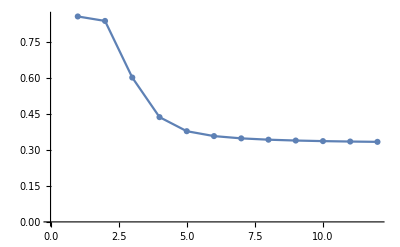

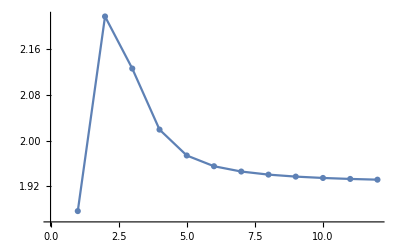

```mathematica
ListPlot[Table[{ssG[[i]]/Δ,stcEG[[i]]},{i,1,Length[ssG]}],Joined->True,PlotMarkers->Automatic]
ListPlot[Table[{ssG[[i]]/Δ,stcIG[[i]]},{i,1,Length[ssG]}],Joined->True,PlotMarkers->Automatic]
```

```mathematica
stI
```

{0.22763,0.37463,0.56084,0.774891,1.00139,1.22448,1.43074,1.61057,1.75821,1.9955,1.99252,1.92958,1.85134,1.8725,1.95303,1.97668,1.94985,1.91628,1.90053}

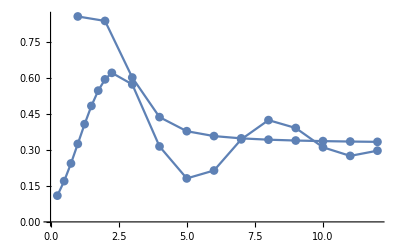

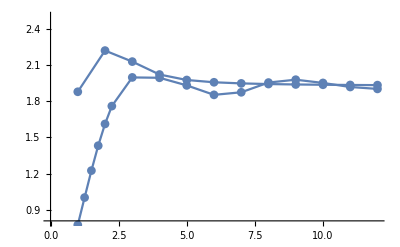

```mathematica
Show[{ListPlot[Table[{ssG[[i]]/Δ,stcEG[[i]]},{i,1,Length[ssG]}],Joined->True,PlotMarkers->Automatic],ListPlot[Table[{ss[[i]]/Δ,stE[[i]]},{i,1,Length[ss]}],Joined->True,PlotMarkers->Automatic]}]
Show[{ListPlot[Table[{ssG[[i]]/Δ,stcIG[[i]]},{i,1,Length[ssG]}],Joined->True,PlotMarkers->Automatic,PlotRange->{0.8,2.5}],ListPlot[Table[{ss[[i]]/Δ,stI[[i]]},{i,1,Length[ss]}],Joined->True,PlotMarkers->Automatic]}]
```

## Contrast dependent surround suppression - pillbox

```mathematica
Δx=1/3;(*degrees/ncells*)
Δ=Δx^-1; (*ncells/degree*)
Nn=IntegerPart[25Δ];(*from -5 to 5 times Δx=4*)
cent=Nn/2;
σFF=(0.125)^2;(*this is the variance*)
σEE=(2Δ/3)^2;
σIE=(4Δ/3)^2;
σEI=(0.01)^2;(*only to the same grid position as projecting neuron*)
σII=(0.01)^2;
k=0.01;
c=1;
(*G[z_,s_]:=1/Sqrt[2π s] Exp[-z^2/(2s)];(*fix normalization because it is discrete*)*)
(*H=h0 Table[G[z-cent,σFF],{z,0,Nn}];*)
G[z_,s_]:=Exp[-z^2/(2s)];
H[l_]:=c Table[(1/(1+Exp[-(x+l/2)/σFF]))(1-1/(1+Exp[-(x-l/2)/σFF])),{x,-Nn/2,Nn/2}]
HG[l_]:=c Table[Exp[-x^2/(2(0.5 l)^2)],{x,-Nn/2,Nn/2}];
WEE=1 Table[G[z-y,σEE],{z,0,Nn},{y,0,Nn}];
WIE=1.25 Table[G[z-y,σIE],{z,0,Nn},{y,0,Nn}];
WEI=-1Table[G[z-y,σEI],{z,0,Nn},{y,0,Nn}];
WII=-0.75 Table[G[z-y,σII],{z,0,Nn},{y,0,Nn}];
```

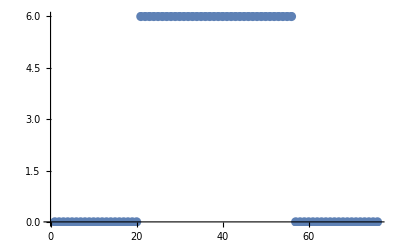

```mathematica
c=6;
s=12Δ;
ListPlot[H[s],PlotRange->All]
```

```mathematica
ϕ[x_]:=k HeavisideTheta[x] x^2.2;
(*ϕ[x_]:=x^2;*)
f[x_List?(Length[#]==Nn+1&)]:=Map[ϕ,x];
```

```mathematica
Clear[X,Y];
tmax=40;
c=6;
s=10Δ;
sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+H[s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+H[s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];
```

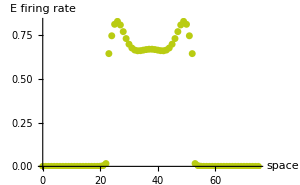
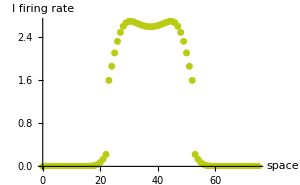

```mathematica
tmax=40;
Row[{ListPlot[Evaluate[sol[[1]][tmax]],DataRange->{0,Nn},PlotRange->All,AxesLabel->{"space","E firing rate"},PlotStyle->ColorData[10]@5,ImageSize->300],ListPlot[Evaluate[sol[[2]][tmax]],DataRange->{0,Nn},PlotRange->All,AxesLabel->{"space","I firing rate"},PlotStyle->ColorData[10]@5,ImageSize->300]}]
```

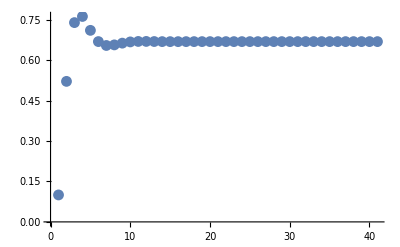

{3.94593,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}

{19.7021,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}

```mathematica
ListPlot[Table[Evaluate[sol[[1]][t]][[IntegerPart[Nn/2]]],{t,0,tmax}],PlotRange->All]
```

```mathematica
Clear[X,Y,s];
tmax=25;
c=31;
stcEc31=ConstantArray[.00001,5];
stcIc31=ConstantArray[.00001,5];
ind=1;
For[s=0.1,s<2,s=s+0.4,{sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+H[Δ s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+H[Δ s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];stcEc31[[ind]]=Evaluate[sol[[1]][tmax]][[IntegerPart[Nn/2]]];stcIc31[[ind]]=Evaluate[sol[[2]][tmax]][[IntegerPart[Nn/2]]];
ind=ind+1;
Print[stcEc31];Print[stcIc31];}]
```

{1.84447×10^-12,0.00001,0.00001,0.00001,0.00001}

{2.04356×10^-12,0.00001,0.00001,0.00001,0.00001}

{1.84447×10^-12,1.26825,0.00001,0.00001,0.00001}

{2.04356×10^-12,7.74363,0.00001,0.00001,0.00001}

{1.84447×10^-12,1.26825,1.26858,0.00001,0.00001}

{2.04356×10^-12,7.74363,7.74498,0.00001,0.00001}

{1.84447×10^-12,1.26825,1.26858,6.34929,0.00001}

{2.04356×10^-12,7.74363,7.74498,33.774,0.00001}

{1.84447×10^-12,1.26825,1.26858,6.34929,5.62402}

{2.04356×10^-12,7.74363,7.74498,33.774,34.8429}

```mathematica
Export["/Users/serena/Dropbox/RubinsizetuningEc31_smalls.csv",stcEc31];
Export["/Users/serena/Dropbox/RubinsizetuningIc31_smalls.csv",stcIc31];
```

```mathematica
ssc={0.1,0.5,1,1.7,2,3,4,5,6,7,8,9,10,11,12}Δ;
```

```mathematica
d1s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc1_smalls.csv","Data"];
d6s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc6_smalls.csv","Data"];
d11s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc11_smalls.csv","Data"];
d21s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc21_smalls.csv","Data"];
d31s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc31_smalls.csv","Data"];
d1=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc1.csv","Data"];
d6=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc6.csv","Data"];
d11=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc11.csv","Data"];
d21=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc21.csv","Data"];
d31=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc31.csv","Data"];
```

```mathematica
ds1=Join[d1s[[1;;2]],{d1[[1]]},{d1s[[5]]},d1[[2;;]]];
ds6=Join[d6s[[1;;2]],{d6[[1]]},{d6s[[5]]},d6[[2;;]]];
ds11=Join[d11s[[1;;2]],{d11[[1]]},{d11s[[5]]},d11[[2;;]]];
ds21=Join[d21s[[1;;2]],{d21[[1]]},{d21s[[5]]},d21[[2;;]]];
ds31=Join[d31s[[1;;2]],{d31[[1]]},{d31s[[5]]},d31[[2;;]]];
```

```mathematica
ll=Length[ds1];
dsall=ConstantArray[0,{5,ll}];
dsall[[1,;;]]=ds1;
dsall[[2,;;]]=ds6;
dsall[[3,;;]]=ds11;
dsall[[4,;;]]=ds21;
dsall[[5,;;]]=ds31;
```

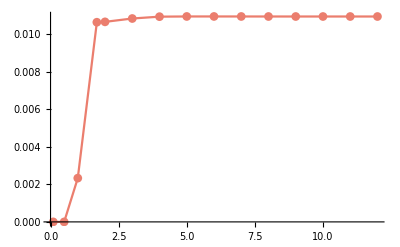
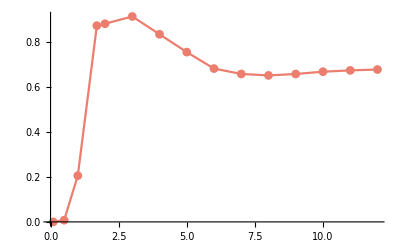
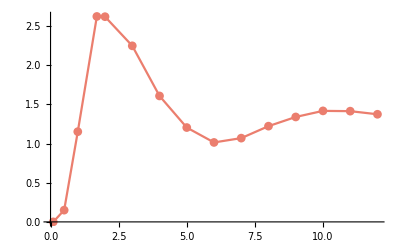
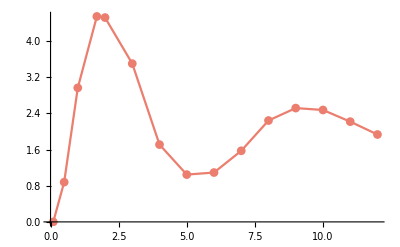
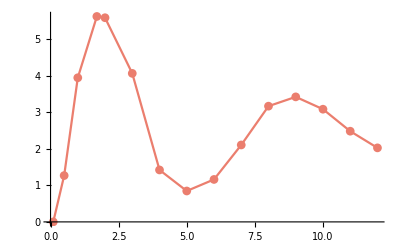

```mathematica
Table[ListPlot[Table[{ssc[[i]]/Δ,dsall[[cc,i]]},{i,1,ll}],Joined->True,PlotMarkers->Automatic,PlotStyle->ColorData[24]],{cc,1,5}]
```

```mathematica
ssc={0.1,0.5,1,1.3,1.7,2,3,4,5,6,7,8,9,10,11,12}Δ;
```

```mathematica
d1s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc1_smalls.csv","Data"];
d6s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc6_smalls.csv","Data"];
d11s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc11_smalls.csv","Data"];
d21s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc21_smalls.csv","Data"];
d31s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc31_smalls.csv","Data"];
d1=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc1.csv","Data"];
d6=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc6.csv","Data"];
d11=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc11.csv","Data"];
d21=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc21.csv","Data"];
d31=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEc31.csv","Data"];
```

```mathematica
ds1=Join[d1s[[1;;2]],{d1[[1]]},d1s[[4;;5]],d1[[2;;]]];
ds6=Join[d6s[[1;;2]],{d6[[1]]},d6s[[4;;5]],d6[[2;;]]];
ds11=Join[d11s[[1;;2]],{d11[[1]]},d11s[[4;;5]],d11[[2;;]]];
ds21=Join[d21s[[1;;2]],{d21[[1]]},d21s[[4;;5]],d21[[2;;]]];
ds31=Join[d31s[[1;;2]],{d31[[1]]},d31s[[4;;5]],d31[[2;;]]];
```

```mathematica
ll=Length[ds1];
```

```mathematica
dsall=ConstantArray[0,{5,ll}];
dsall[[1,;;]]=ds1;
dsall[[2,;;]]=ds6;
dsall[[3,;;]]=ds11;
dsall[[4,;;]]=ds21;
dsall[[5,;;]]=ds31;
```

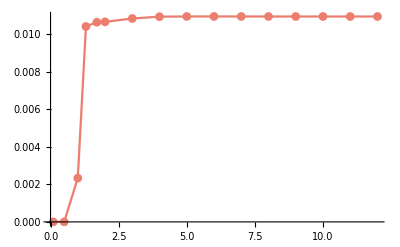
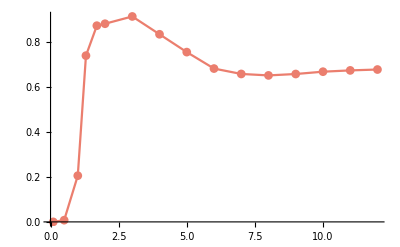
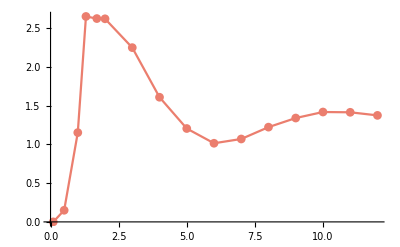
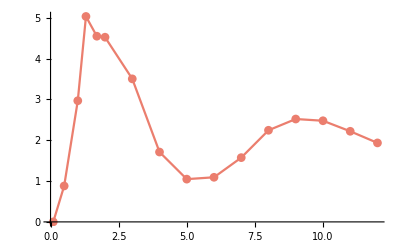
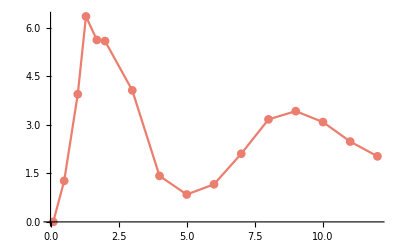

```mathematica
Table[ListPlot[Table[{ssc[[i]]/Δ,dsall[[cc,i]]},{i,1,ll}],Joined->True,PlotMarkers->Automatic,PlotStyle->ColorData[24]],{cc,1,5}]
```

## Contrast dependent surround suppression - Gaussian, σaI only to the same grid position as projecting neuron

```mathematica
Δx=1/3;(*degrees/ncells*)
Δ=Δx^-1; (*ncells/degree*)
Nn=IntegerPart[25Δ];(*from -5 to 5 times Δx=4*)
cent=Nn/2;
(*σFF=(0.125)^2;*)(*this is the variance*)
σEE=(2Δ/3)^2;
σIE=(4Δ/3)^2;
σEI=(0.01)^2;(*only to the same grid position as projecting neuron*)
σII=(0.01)^2;(*only to the same grid position as projecting neuron*)
k=0.01;
c=1;
(*G[z_,s_]:=1/Sqrt[2π s] Exp[-z^2/(2s)];(*fix normalization because it is discrete*)*)
(*H=h0 Table[G[z-cent,σFF],{z,0,Nn}];*)
G[z_,s_]:=Exp[-z^2/(2s)];
(*H[l_]:=c Table[(1/(1+Exp[-(x+l/2)/σFF]))(1-1/(1+Exp[-(x-l/2)/σFF])),{x,-Nn/2,Nn/2}]*)
HG[l_]:=c Table[Exp[-x^2/(2(0.5 l)^2)],{x,-Nn/2,Nn/2}];
WEE=Quiet[1 Table[G[z-y,σEE],{z,0,Nn},{y,0,Nn}]];
WIE=Quiet[1.25 Table[G[z-y,σIE],{z,0,Nn},{y,0,Nn}]];
WEI=Quiet[-1Table[G[z-y,σEI],{z,0,Nn},{y,0,Nn}]];
WII=Quiet[-0.75 Table[G[z-y,σII],{z,0,Nn},{y,0,Nn}]];
ϕ[x_]:=k HeavisideTheta[x] x^2.2;
(*ϕ[x_]:=x^2;*)
f[x_List?(Length[#]==Nn+1&)]:=Map[ϕ,x];
```

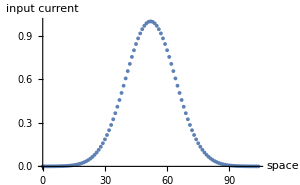
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
s=6Δ;
Quiet[Row[{ListPlot[HG[s],PlotRange->All,ImageSize->300,DataRange->{0,Nn},AxesLabel->{"space","input current"}],MatrixPlot[WEE,PlotLegends->Automatic,ImageSize->150,PlotLabel->"EE connectivity"],MatrixPlot[WIE,PlotLegends->Automatic,ImageSize->150,PlotLabel->"IE connectivity"],MatrixPlot[WEI,PlotLegends->Automatic,ImageSize->150,PlotLabel->"EI connectivity"],MatrixPlot[WII,PlotLegends->Automatic,ImageSize->150,PlotLabel->"II connectivity"]}]]
```

```mathematica
Clear[X,Y];
tmax=40;
c=6;
s=10Δ;
sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+HG[s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+HG[s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];
```

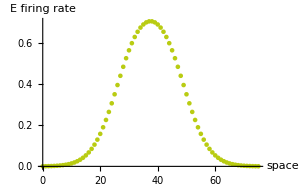
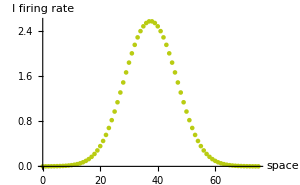

```mathematica
tmax=40;
Row[{ListPlot[Evaluate[sol[[1]][tmax]],DataRange->{0,Nn},PlotRange->All,AxesLabel->{"space","E firing rate"},PlotStyle->ColorData[10]@5,ImageSize->300],ListPlot[Evaluate[sol[[2]][tmax]],DataRange->{0,Nn},PlotRange->All,AxesLabel->{"space","I firing rate"},PlotStyle->ColorData[10]@5,ImageSize->300]}]
```

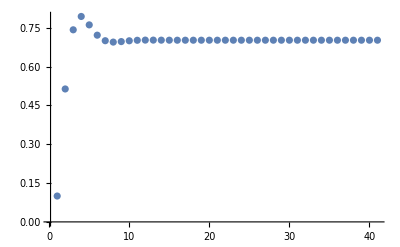

```mathematica
ListPlot[Table[Evaluate[sol[[1]][t]][[IntegerPart[Nn/2]]],{t,0,tmax}],PlotRange->All]
```

```mathematica
Clear[X,Y,s];
tmax=40;
c=31;
stcEGc=ConstantArray[.00001,10];
stcIGc=ConstantArray[.00001,10];
ind=1;
For[s=0.1,s<4,s=s+0.4,{sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+HG[Δ s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+HG[Δ s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];stcEGc[[ind]]=Evaluate[sol[[1]][tmax]][[IntegerPart[Nn/2]]];stcIGc[[ind]]=Evaluate[sol[[2]][tmax]][[IntegerPart[Nn/2]]];
ind=ind+1;
Print[stcEGc];Print[stcIGc];}]
```

```mathematica
Export["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/RubinComparison/RubinsizetuningEGc31_smalls.csv",stcEGc];
Export["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/RubinComparison/RubinsizetuningIGc31_smalls.csv",stcIGc];
```

```mathematica
ssc=Table[s Δ,{s,0.1,4,0.4}];
d6s=Flatten@Import["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/RubinComparison/RubinsizetuningEGc6_smalls.csv","Data"];
d11s=Flatten@Import["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/RubinComparison/RubinsizetuningEGc11_smalls.csv","Data"];
d21s=Flatten@Import["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/RubinComparison/RubinsizetuningEGc21_smalls.csv","Data"];
d31s=Flatten@Import["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/RubinComparison/RubinsizetuningEGc31_smalls.csv","Data"];
```

```mathematica
ll=Length[d6s];
dsall=ConstantArray[0,{4,ll}];
dsall[[1,;;]]=d6s;
dsall[[2,;;]]=d11s;
dsall[[3,;;]]=d21s;
dsall[[4,;;]]=d31s;
```

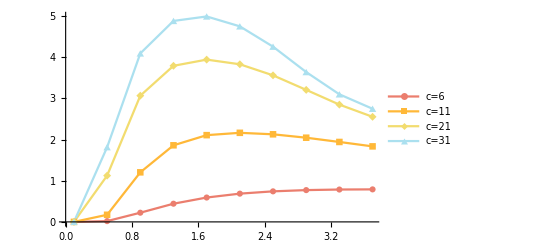

```mathematica
ListPlot[Table[Table[{ssc[[i]]/Δ,dsall[[cc,i]]},{i,1,ll}],{cc,1,4}],Joined->True,PlotMarkers->Automatic,PlotStyle->ColorData[24],PlotLegends->{"c=6","c=11","c=21","c=31"}]
```

## Contrast dependent surround suppression - Gaussian, σaI to the same grid position and next one, input current wide

```mathematica
Δx=1/3;(*degrees/ncells*)
Δ=Δx^-1; (*ncells/degree*)
Nn=IntegerPart[25Δ];(*from -5 to 5 times Δx=4*)
cent=Nn/2;
(*σFF=(0.125)^2;*)(*this is the variance, only relevant for pillbox-shaped input)*)
σEE=(2Δ/3)^2;
σIE=(4Δ/3)^2;
σEI=(0.3)^2;
σII=(0.3)^2;
k=0.01;
c=1;
(*G[z_,s_]:=1/Sqrt[2π s] Exp[-z^2/(2s)];(*fix normalization because it is discrete*)*)
(*H=h0 Table[G[z-cent,σFF],{z,0,Nn}];*)
G[z_,s_]:=Exp[-z^2/(2s)];
(*H[l_]:=c Table[(1/(1+Exp[-(x+l/2)/σFF]))(1-1/(1+Exp[-(x-l/2)/σFF])),{x,-Nn/2,Nn/2}]*)(*pillbox-shaped input*)
HG[l_]:=c Table[Exp[-x^2/(2(0.5 l)^2)],{x,-Nn/2,Nn/2}];
WEE=Quiet[1 Table[G[z-y,σEE],{z,0,Nn},{y,0,Nn}]];
WIE=Quiet[1.25 Table[G[z-y,σIE],{z,0,Nn},{y,0,Nn}]];
WEI=Quiet[-1Table[G[z-y,σEI],{z,0,Nn},{y,0,Nn}]];
WII=Quiet[-0.75 Table[G[z-y,σII],{z,0,Nn},{y,0,Nn}]];
ϕ[x_]:=k HeavisideTheta[x] x^2.2;
(*ϕ[x_]:=x^2;*)
f[x_List?(Length[#]==Nn+1&)]:=Map[ϕ,x];
```

75

-0.75

0.

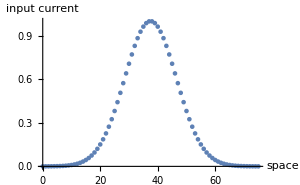
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
s=6Δ;
Nn
WII[[1,1]]
WII[[1,2]]
Quiet[Row[{ListPlot[HG[s],PlotRange->All,ImageSize->300,DataRange->{0,Nn},AxesLabel->{"space","input current"}],MatrixPlot[WEE,PlotLegends->Automatic,ImageSize->150,PlotLabel->"EE connectivity"],MatrixPlot[WIE,PlotLegends->Automatic,ImageSize->150,PlotLabel->"IE connectivity"],MatrixPlot[WEI,PlotLegends->Automatic,ImageSize->150,PlotLabel->"EI connectivity"],MatrixPlot[WII,PlotLegends->Automatic,ImageSize->150,PlotLabel->"II connectivity"]}]]
```

```mathematica
Clear[X,Y];
tmax=40;
c=6;
s=10Δ;
sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+HG[s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+HG[s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];
```

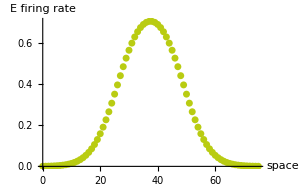
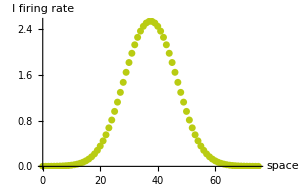

```mathematica
tmax=40;
Row[{ListPlot[Evaluate[sol[[1]][tmax]],DataRange->{0,Nn},PlotRange->All,AxesLabel->{"space","E firing rate"},PlotStyle->ColorData[10]@5,ImageSize->300],ListPlot[Evaluate[sol[[2]][tmax]],DataRange->{0,Nn},PlotRange->All,AxesLabel->{"space","I firing rate"},PlotStyle->ColorData[10]@5,ImageSize->300]}]
```

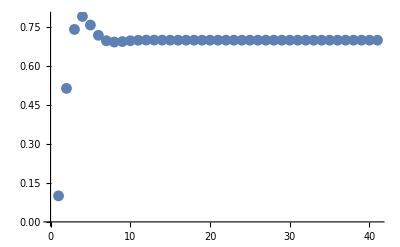

```mathematica
ListPlot[Table[Evaluate[sol[[1]][t]][[IntegerPart[Nn/2]]],{t,0,tmax}],PlotRange->All]
```

```mathematica
Clear[X,Y,s];
tmax=40;
c=31;
stcEGc=ConstantArray[.00001,10];
stcIGc=ConstantArray[.00001,10];
ind=1;
For[s=0.1,s<4,s=s+0.4,{sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+HG[Δ s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+HG[Δ s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False(*,"EquationSimplification"->"Residual"*)}];stcEGc[[ind]]=Evaluate[sol[[1]][tmax]][[IntegerPart[Nn/2]]];stcIGc[[ind]]=Evaluate[sol[[2]][tmax]][[IntegerPart[Nn/2]]];
ind=ind+1;
Print[stcEGc];Print[stcIGc];}]
```

```mathematica
Export["/Users/serena/Dropbox/RubinsizetuningEGc31_sigmaAIlarger.csv",stcEGc];
Export["/Users/serena/Dropbox/RubinsizetuningIGc31_sigmaAIlarger.csv",stcIGc];
```

```mathematica
d6s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEGc6_sigmaAIlarger.csv","Data"];
d11s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEGc11_sigmaAIlarger.csv","Data"];
d21s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEGc21_sigmaAIlarger.csv","Data"];
d31s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEGc31_sigmaAIlarger.csv","Data"];
```

```mathematica
ssc=Table[s Δ,{s,0.1,4,0.4}];
ll=Length[d6s];
dsall=ConstantArray[0,{4,ll}];
dsall[[1,;;]]=d6s;
dsall[[2,;;]]=d11s;
dsall[[3,;;]]=d21s;
dsall[[4,;;]]=d31s;
```

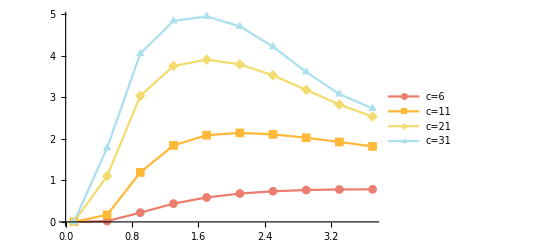

```mathematica
ListPlot[Table[Table[{ssc[[i]]/Δ,dsall[[cc,i]]},{i,1,ll}],{cc,1,4}],Joined->True,PlotMarkers->Automatic,PlotStyle->ColorData[24],PlotLegends->{"c=6","c=11","c=21","c=31"}]
```

## Contrast dependent surround suppression - Gaussian, σaI as large as σEE

```mathematica
Δx=1/3;(*degrees/ncells*)
Δ=Δx^-1; (*ncells/degree*)
Nn=IntegerPart[25Δ];(*from -5 to 5 times Δx=4*)
cent=Nn/2;
(*σFF=(0.125)^2;*)(*this is the variance*)
σEE=(2Δ/3)^2;
σIE=(4Δ/3)^2;
σEI=(2Δ/3)^2;
σII=(2Δ/3)^2;
k=0.01;
c=1;
(*G[z_,s_]:=1/Sqrt[2π s] Exp[-z^2/(2s)];(*fix normalization because it is discrete*)*)
(*H=h0 Table[G[z-cent,σFF],{z,0,Nn}];*)
G[z_,s_]:=Exp[-z^2/(2s)];
(*H[l_]:=c Table[(1/(1+Exp[-(x+l/2)/σFF]))(1-1/(1+Exp[-(x-l/2)/σFF])),{x,-Nn/2,Nn/2}]*)
HG[l_]:=c Table[Exp[-x^2/(2(0.5 l)^2)],{x,-Nn/2,Nn/2}];
WEE=1 Table[G[z-y,σEE],{z,0,Nn},{y,0,Nn}];
WIE=1.25 Table[G[z-y,σIE],{z,0,Nn},{y,0,Nn}];
WEI=-1Table[G[z-y,σEI],{z,0,Nn},{y,0,Nn}];
WII=-0.75 Table[G[z-y,σII],{z,0,Nn},{y,0,Nn}];
ϕ[x_]:=k HeavisideTheta[x] x^2.2;
(*ϕ[x_]:=x^2;*)
f[x_List?(Length[#]==Nn+1&)]:=Map[ϕ,x];
```

```mathematica
s=6Δ;
Nn
WII[[1,1]]
WII[[1,2]]
Quiet[Row[{ListPlot[HG[s],PlotRange->All,ImageSize->300,DataRange->{0,Nn},AxesLabel->{"space","input current"}],MatrixPlot[WEE,PlotLegends->Automatic,ImageSize->150,PlotLabel->"EE connectivity"],MatrixPlot[WIE,PlotLegends->Automatic,ImageSize->150,PlotLabel->"IE connectivity"],MatrixPlot[WEI,PlotLegends->Automatic,ImageSize->150,PlotLabel->"EI connectivity"],MatrixPlot[WII,PlotLegends->Automatic,ImageSize->150,PlotLabel->"II connectivity"]}]]
```

75

-0.75

-0.661873

-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Clear[X,Y,s];
tmax=40;
c=31;
stcEGc=ConstantArray[.00001,10];
stcIGc=ConstantArray[.00001,10];
ind=1;
For[s=0.1,s<4,s=s+0.4,{sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+HG[Δ s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+HG[Δ s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False,"EquationSimplification"->"Residual"}];stcEGc[[ind]]=Evaluate[sol[[1]][tmax]][[IntegerPart[Nn/2]]];stcIGc[[ind]]=Evaluate[sol[[2]][tmax]][[IntegerPart[Nn/2]]];
ind=ind+1;
Print[stcEGc];Print[stcIGc];}]
```

```mathematica
Export["/Users/serena/Dropbox/RubinsizetuningEGc31_sigmaAIlarge.csv",stcEGc];
Export["/Users/serena/Dropbox/RubinsizetuningIGc31_sigmaAIlarge.csv",stcIGc];
```

```mathematica
d11s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEGc11_sigmaAIlarge.csv","Data"];
d21s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEGc21_sigmaAIlarge.csv","Data"];
d31s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEGc31_sigmaAIlarge.csv","Data"];
```

```mathematica
ssc=Table[s Δ,{s,0.1,4,0.4}];
ll=Length[d11s];
dsall=ConstantArray[0,{3,ll}];
dsall[[1,;;]]=d11s;
dsall[[2,;;]]=d21s;
dsall[[3,;;]]=d31s;
```

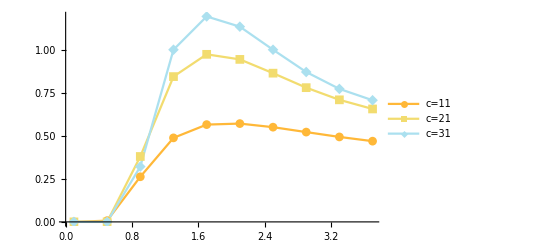

```mathematica
ListPlot[Table[Table[{ssc[[i]]/Δ,dsall[[cc,i]]},{i,1,ll}],{cc,1,3}],Joined->True,PlotMarkers->Automatic,PlotStyle->ColorData[24]/@{2,3,4},PlotLegends->{"c=11","c=21","c=31"}]
```

can’t really see contrast-dependent size-tuning

## Contrast dependent surround suppression - Gaussian, σaI half EE

```mathematica
Δx=1/3;(*degrees/ncells*)
Δ=Δx^-1; (*ncells/degree*)
Nn=IntegerPart[25Δ];(*from -5 to 5 times Δx=4*)
cent=Nn/2;
σFF=(0.125)^2;(*this is the variance*)
σEE=(2Δ/3)^2;
σIE=(4Δ/3)^2;
σEI=(Δ/3)^2;
σII=(Δ/3)^2;
k=0.01;
c=1;
(*G[z_,s_]:=1/Sqrt[2π s] Exp[-z^2/(2s)];(*fix normalization because it is discrete*)*)
(*H=h0 Table[G[z-cent,σFF],{z,0,Nn}];*)
G[z_,s_]:=Exp[-z^2/(2s)];
H[l_]:=c Table[(1/(1+Exp[-(x+l/2)/σFF]))(1-1/(1+Exp[-(x-l/2)/σFF])),{x,-Nn/2,Nn/2}]
HG[l_]:=c Table[Exp[-x^2/(2(0.5 l)^2)],{x,-Nn/2,Nn/2}];
WEE=1 Table[G[z-y,σEE],{z,0,Nn},{y,0,Nn}];
WIE=1.25 Table[G[z-y,σIE],{z,0,Nn},{y,0,Nn}];
WEI=-1Table[G[z-y,σEI],{z,0,Nn},{y,0,Nn}];
WII=-0.75 Table[G[z-y,σII],{z,0,Nn},{y,0,Nn}];
ϕ[x_]:=k HeavisideTheta[x] x^2.2;
(*ϕ[x_]:=x^2;*)
f[x_List?(Length[#]==Nn+1&)]:=Map[ϕ,x];
```

75

-0.75

-0.454898

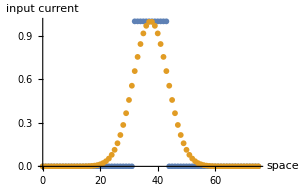
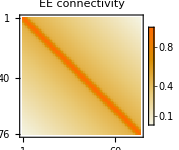
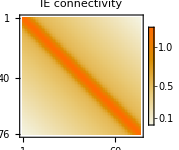
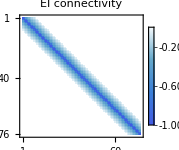
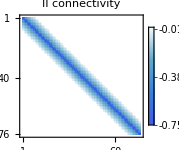

```mathematica
s=4Δ;
Nn
WII[[1,1]]
WII[[1,2]]
Row[{ListPlot[{H[s],HG[s]},PlotRange->All,ImageSize->300,DataRange->{0,Nn},AxesLabel->{"space","input current"}],MatrixPlot[WEE,PlotLegends->Automatic,ImageSize->150,PlotLabel->"EE connectivity"],MatrixPlot[WIE,PlotLegends->Automatic,ImageSize->150,PlotLabel->"IE connectivity"],MatrixPlot[WEI,PlotLegends->Automatic,ImageSize->150,PlotLabel->"EI connectivity"],MatrixPlot[WII,PlotLegends->Automatic,ImageSize->150,PlotLabel->"II connectivity"]}]
```

```mathematica
Clear[X,Y,s];
tmax=40;
c=31;
stcEGc=ConstantArray[.00001,10];
stcIGc=ConstantArray[.00001,10];
ind=1;
For[s=0.1,s<4,s=s+0.4,{sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+HG[Δ s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+HG[Δ s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False,"EquationSimplification"->"Residual"}];stcEGc[[ind]]=Evaluate[sol[[1]][tmax]][[IntegerPart[Nn/2]]];stcIGc[[ind]]=Evaluate[sol[[2]][tmax]][[IntegerPart[Nn/2]]];
ind=ind+1;
Print[stcEGc];Print[stcIGc];}]
```

```mathematica
Export["/Users/serena/Dropbox/RubinsizetuningEGc31_sigmaAIhalfEE.csv",stcEGc];
Export["/Users/serena/Dropbox/RubinsizetuningIGc31_sigmaAIhalfEE.csv",stcIGc];
```

```mathematica
d11s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEGc11_sigmaAIhalfEE.csv","Data"];
d21s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEGc21_sigmaAIhalfEE.csv","Data"];
d31s=Flatten@Import["/Users/serena/Dropbox/RubinsizetuningEGc31_sigmaAIhalfEE.csv","Data"];
```

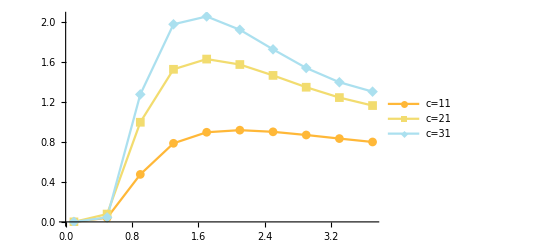

```mathematica
ssc=Table[s Δ,{s,0.1,4,0.4}];
ll=Length[d11s];
dsall=ConstantArray[0,{3,ll}];
dsall[[1,;;]]=d11s;
dsall[[2,;;]]=d21s;
dsall[[3,;;]]=d31s;
ListPlot[Table[Table[{ssc[[i]]/Δ,dsall[[cc,i]]},{i,1,ll}],{cc,1,3}],Joined->True,PlotMarkers->Automatic,PlotStyle->ColorData[24]/@{2,3,4},PlotLegends->{"c=11","c=21","c=31"}]
```

can’t really see contrast-dependent size-tuning

## Contrast dependent surround suppression - Gaussian, σaI only to the same grid position as projecting neuron, input width smaller

```mathematica
Δx=1/3;(*degrees/ncells*)
Δ=Δx^-1; (*ncells/degree*)
Nn=IntegerPart[25Δ];(*from -5 to 5 times Δx=4*)
cent=Nn/2;
(*σFF=(0.125)^2;*)(*this is the variance*)
σEE=(2Δ/3)^2;
σIE=(4Δ/3)^2;
σEI=(Δ/3)^2;(*only to the same grid position as projecting neuron*)
σII=(Δ/3)^2;(*only to the same grid position as projecting neuron*)
k=0.01;
σff=(2Δ/3)^2;
c=1;
(*G[z_,s_]:=1/Sqrt[2π s] Exp[-z^2/(2s)];(*fix normalization because it is discrete*)*)
(*H=h0 Table[G[z-cent,σFF],{z,0,Nn}];*)
G[z_,s_]:=Exp[-z^2/(2s)];
(*H[l_]:=c Table[(1/(1+Exp[-(x+l/2)/σFF]))(1-1/(1+Exp[-(x-l/2)/σFF])),{x,-Nn/2,Nn/2}]*)
HG[l_]:=c Table[Exp[-x^2/(2((0.5 l)^2+σff^2))],{x,-Nn/2,Nn/2}];(*smaller input width*)
WEE=Quiet[1 Table[G[z-y,σEE],{z,0,Nn},{y,0,Nn}]];
WIE=Quiet[1.25 Table[G[z-y,σIE],{z,0,Nn},{y,0,Nn}]];
WEI=Quiet[-1Table[G[z-y,σEI],{z,0,Nn},{y,0,Nn}]];
WII=Quiet[-0.75 Table[G[z-y,σII],{z,0,Nn},{y,0,Nn}]];
ϕ[x_]:=k HeavisideTheta[x] x^2.2;
(*ϕ[x_]:=x^2;*)
f[x_List?(Length[#]==Nn+1&)]:=Map[ϕ,x];
```

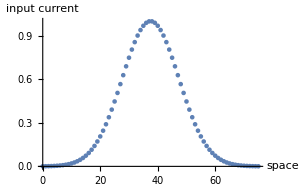
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
s=6Δ;
Quiet[Row[{ListPlot[HG[s],PlotRange->All,ImageSize->300,DataRange->{0,Nn},AxesLabel->{"space","input current"}],MatrixPlot[WEE,PlotLegends->Automatic,ImageSize->150,PlotLabel->"EE connectivity"],MatrixPlot[WIE,PlotLegends->Automatic,ImageSize->150,PlotLabel->"IE connectivity"],MatrixPlot[WEI,PlotLegends->Automatic,ImageSize->150,PlotLabel->"EI connectivity"],MatrixPlot[WII,PlotLegends->Automatic,ImageSize->150,PlotLabel->"II connectivity"]}]]
```

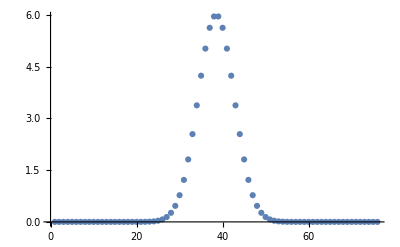

```mathematica
c=6;
s=7Δ;
ListPlot[HG[s],PlotRange->All]
```

```mathematica
Clear[X,Y];
tmax=40;
c=6;
s=10Δ;
sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+HG[s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+HG[s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];
```

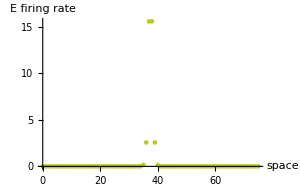
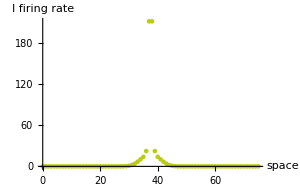

```mathematica
tmax=40;
Row[{ListPlot[Evaluate[sol[[1]][tmax]],DataRange->{0,Nn},PlotRange->All,AxesLabel->{"space","E firing rate"},PlotStyle->ColorData[10]@5,ImageSize->300],ListPlot[Evaluate[sol[[2]][tmax]],DataRange->{0,Nn},PlotRange->All,AxesLabel->{"space","I firing rate"},PlotStyle->ColorData[10]@5,ImageSize->300]}]
```

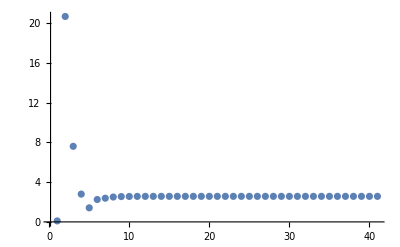

```mathematica
ListPlot[Table[Evaluate[sol[[1]][t]][[IntegerPart[Nn/2]]],{t,0,tmax}],PlotRange->All]
```

```mathematica
Clear[X,Y,s];
tmax=40;
c=31;
stcEGc=ConstantArray[.00001,10];
stcIGc=ConstantArray[.00001,10];
ind=1;
For[s=0.1,s<4,s=s+0.4,(*changing this?*){sol=NDSolveValue[{X'[t]==-X[t]+f[WEE.X[t]+WEI.Y[t]+HG[Δ s]],Y'[t]==-Y[t]+f[WIE.X[t]+WII.Y[t]+HG[Δ s]],X[0]==ConstantArray[.1,Nn+1],Y[0]==ConstantArray[.1,Nn+1]},{X,Y},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];stcEGc[[ind]]=Evaluate[sol[[1]][tmax]][[IntegerPart[Nn/2]]];stcIGc[[ind]]=Evaluate[sol[[2]][tmax]][[IntegerPart[Nn/2]]];
ind=ind+1;
Print[stcEGc];Print[stcIGc];}]
```

General::munfl: Exp[-781250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-740139.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-700139.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{1.68411×10^-14,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001}

{1.86588×10^-14,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001}

{1.68411×10^-14,3.33084×10^-11,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001}

{1.86588×10^-14,8.78847×10^-11,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001}

{1.68411×10^-14,3.33084×10^-11,0.00527513,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001}

{1.86588×10^-14,8.78847×10^-11,0.0142735,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001}

{1.68411×10^-14,3.33084×10^-11,0.00527513,0.342455,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001}

{1.86588×10^-14,8.78847×10^-11,0.0142735,1.19857,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001}

{1.68411×10^-14,3.33084×10^-11,0.00527513,0.342455,0.836708,0.00001,0.00001,0.00001,0.00001,0.00001}

{1.86588×10^-14,8.78847×10^-11,0.0142735,1.19857,3.6019,0.00001,0.00001,0.00001,0.00001,0.00001}

{1.68411×10^-14,3.33084×10^-11,0.00527513,0.342455,0.836708,1.28537,0.00001,0.00001,0.00001,0.00001}

{1.86588×10^-14,8.78847×10^-11,0.0142735,1.19857,3.6019,5.89101,0.00001,0.00001,0.00001,0.00001}

{1.68411×10^-14,3.33084×10^-11,0.00527513,0.342455,0.836708,1.28537,1.81392,0.00001,0.00001,0.00001}

{1.86588×10^-14,8.78847×10^-11,0.0142735,1.19857,3.6019,5.89101,8.39531,0.00001,0.00001,0.00001}

{1.68411×10^-14,3.33084×10^-11,0.00527513,0.342455,0.836708,1.28537,1.81392,2.38146,0.00001,0.00001}

{1.86588×10^-14,8.78847×10^-11,0.0142735,1.19857,3.6019,5.89101,8.39531,11.0671,0.00001,0.00001}

{1.68411×10^-14,3.33084×10^-11,0.00527513,0.342455,0.836708,1.28537,1.81392,2.38146,2.91918,0.00001}

{1.86588×10^-14,8.78847×10^-11,0.0142735,1.19857,3.6019,5.89101,8.39531,11.0671,13.7009,0.00001}

{1.68411×10^-14,3.33084×10^-11,0.00527513,0.342455,0.836708,1.28537,1.81392,2.38146,2.91918,3.38792}

{1.86588×10^-14,8.78847×10^-11,0.0142735,1.19857,3.6019,5.89101,8.39531,11.0671,13.7009,16.1432}

```mathematica
Export["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/RubinComparison/RubinsizetuningEGc31_smalls_smallin.csv",stcEGc];
Export["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/RubinComparison/RubinsizetuningIGc31_smalls_smallin.csv",stcIGc];
```

```mathematica
ssc=Table[s Δ,{s,0.1,4,0.4}];
d6s=Flatten@Import["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/RubinComparison/RubinsizetuningEGc6_smalls_smallin.csv","Data"];
d11s=Flatten@Import["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/RubinComparison/RubinsizetuningEGc11_smalls_smallin.csv","Data"];
d21s=Flatten@Import["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/RubinComparison/RubinsizetuningEGc21_smalls_smallin.csv","Data"];
d31s=Flatten@Import["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/RubinComparison/RubinsizetuningEGc31_smalls_smallin.csv","Data"];
```

```mathematica
d31s=Flatten@Import["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/RubinComparison/RubinsizetuningEGc31_smalls_smallin.csv","Data"];
```

```mathematica
ll=Length[d6s];
dsall=ConstantArray[0,{4,ll}];
dsall[[1,;;]]=d6s;
dsall[[2,;;]]=d11s;
dsall[[3,;;]]=d21s;
dsall[[4,;;]]=d31s;
```

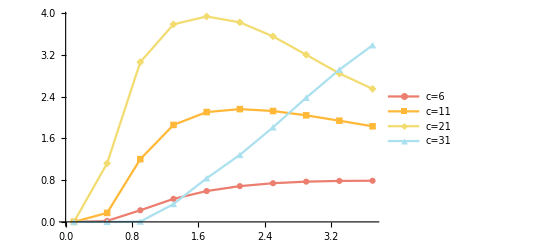

```mathematica
ListPlot[Table[Table[{ssc[[i]]/Δ,dsall[[cc,i]]},{i,1,ll}],{cc,1,4}],Joined->True,PlotMarkers->Automatic,PlotStyle->ColorData[24],PlotLegends->{"c=6","c=11","c=21","c=31"}]
```